```mathematica
ϵl=.;δ=.;Δ=.;
```

```mathematica
h=({{0, 0, Δ, ϵl-δ, 0, 0}, {0, 0, 0, 0, ϵl, 0}, {Δ, 0, 0, 0, 0, ϵl+δ}, {ϵl-δ, 0, 0, 0, 0, Δ}, {0, ϵl, 0, 0, 0, 0}, {0, 0, ϵl+δ, Δ, 0, 0}});J=({{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}, {-1, 0, 0, 0, 0, 0}, {0, -1, 0, 0, 0, 0}, {0, 0, -1, 0, 0, 0}});
```

```mathematica
res=Eigensystem[h.J]
```

{{-ϵl,ϵl,-δ-√(-Δ^2+ϵl^2),δ-√(-Δ^2+ϵl^2),-δ+√(-Δ^2+ϵl^2),δ+√(-Δ^2+ϵl^2)},{{0,1,0,0,0,0},{0,0,0,0,1,0},{0,0,-(-ϵl-√(-Δ^2+ϵl^2))/Δ,1,0,0},{-(-ϵl-√(-Δ^2+ϵl^2))/Δ,0,0,0,0,1},{0,0,-(-ϵl+√(-Δ^2+ϵl^2))/Δ,1,0,0},{-(-ϵl+√(-Δ^2+ϵl^2))/Δ,0,0,0,0,1}}}

```mathematica
n1=.;n2=.;n3=.;n4=.;n5=.;n6=.;
```

```mathematica
Norma=({{n1, 0, 0, 0, 0, 0}, {0, n2, 0, 0, 0, 0}, {0, 0, n3, 0, 0, 0}, {0, 0, 0, n4, 0, 0}, {0, 0, 0, 0, n5, 0}, {0, 0, 0, 0, 0, n6}});
```

```mathematica
P=({{1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0}});
```

```mathematica
Mat=(Transpose[res[[2]]].Norma).P;MatrixForm[Mat]
```

(0 | 0 | -(n4 (-ϵl-√(-Δ^2+ϵl^2)))/Δ | 0 | -(n6 (-ϵl+√(-Δ^2+ϵl^2)))/Δ | 0
n1 | 0 | 0 | 0 | 0 | 0
0 | -(n3 (-ϵl-√(-Δ^2+ϵl^2)))/Δ | 0 | 0 | 0 | -(n5 (-ϵl+√(-Δ^2+ϵl^2)))/Δ
0 | n3 | 0 | 0 | 0 | n5
0 | 0 | 0 | n2 | 0 | 0
0 | 0 | n4 | 0 | n6 | 0)

```mathematica
MatrixForm[FullSimplify[Transpose[Mat].J.Mat]]
```

(0 | 0 | 0 | n1 n2 | 0 | 0
0 | 0 | 0 | 0 | (2 n3 n6 √(-Δ^2+ϵl^2))/Δ | 0
0 | 0 | 0 | 0 | 0 | (2 n4 n5 √(-Δ^2+ϵl^2))/Δ
-n1 n2 | 0 | 0 | 0 | 0 | 0
0 | -(2 n3 n6 √(-Δ^2+ϵl^2))/Δ | 0 | 0 | 0 | 0
0 | 0 | -(2 n4 n5 √(-Δ^2+ϵl^2))/Δ | 0 | 0 | 0)

```mathematica
n2=n1;n6=-(n3 (-ϵl-√(-Δ^2+ϵl^2)))/Δ;n5=-(n4 (-ϵl-√(-Δ^2+ϵl^2)))/Δ;
```

```mathematica
n1=1;
```

```mathematica
n3=1/Sqrt[((2 (n6/n3) √(-Δ^2+ϵl^2))/Δ)];
```

```mathematica
n4=1/Sqrt[((2 (n5/n4) √(-Δ^2+ϵl^2))/Δ)];
```

```mathematica
MatrixForm[FullSimplify[Transpose[Mat].J.Mat]]
```

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0)

```mathematica
MatrixForm[Mat]
```

(0 | 0 | -(-ϵl-√(-Δ^2+ϵl^2))/(√2 Δ √(-(√(-Δ^2+ϵl^2) (-ϵl-√(-Δ^2+ϵl^2)))/Δ^2)) | 0 | ((-ϵl-√(-Δ^2+ϵl^2)) (-ϵl+√(-Δ^2+ϵl^2)))/(√2 Δ^2 √(-(√(-Δ^2+ϵl^2) (-ϵl-√(-Δ^2+ϵl^2)))/Δ^2)) | 0
1 | 0 | 0 | 0 | 0 | 0
0 | -(-ϵl-√(-Δ^2+ϵl^2))/(√2 Δ √(-(√(-Δ^2+ϵl^2) (-ϵl-√(-Δ^2+ϵl^2)))/Δ^2)) | 0 | 0 | 0 | ((-ϵl-√(-Δ^2+ϵl^2)) (-ϵl+√(-Δ^2+ϵl^2)))/(√2 Δ^2 √(-(√(-Δ^2+ϵl^2) (-ϵl-√(-Δ^2+ϵl^2)))/Δ^2))
0 | 1/(√2 √(-(√(-Δ^2+ϵl^2) (-ϵl-√(-Δ^2+ϵl^2)))/Δ^2)) | 0 | 0 | 0 | -(-ϵl-√(-Δ^2+ϵl^2))/(√2 Δ √(-(√(-Δ^2+ϵl^2) (-ϵl-√(-Δ^2+ϵl^2)))/Δ^2))
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1/(√2 √(-(√(-Δ^2+ϵl^2) (-ϵl-√(-Δ^2+ϵl^2)))/Δ^2)) | 0 | -(-ϵl-√(-Δ^2+ϵl^2))/(√2 Δ √(-(√(-Δ^2+ϵl^2) (-ϵl-√(-Δ^2+ϵl^2)))/Δ^2)) | 0)

```mathematica
Mat[[All,1]]
```

{0,1,0,0,0,0}

```mathematica
FullSimplify[(h.J.Mat[[All,1]])[[2]]/Mat[[2,1]]]
```

-ϵl

```mathematica
FullSimplify[(h.J.Mat[[All,2]])[[3]]/Mat[[3,2]]]
```

-δ-√(-Δ^2+ϵl^2)

```mathematica
FullSimplify[(h.J.Mat[[All,3]])[[1]]/Mat[[1,3]]]
```

δ-√(-Δ^2+ϵl^2)

```mathematica
FullSimplify[(h.J.Mat[[All,4]])[[5]]/Mat[[5,4]]]
```

ϵl

```mathematica
FullSimplify[(h.J.Mat[[All,5]])[[1]]/Mat[[1,5]]]
```

δ+√(-Δ^2+ϵl^2)

```mathematica
FullSimplify[(h.J.Mat[[All,6]])[[3]]/Mat[[3,6]]]
```

-δ+√(-Δ^2+ϵl^2)

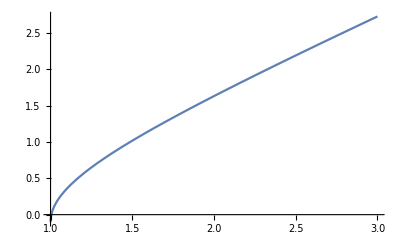

```mathematica
Plot[-δ+√(-Δ^2+ϵl^2)/.Δ->1/.δ->0.1,{Δ,1,3}]
```